Analysing Quantum Systems With(out) Machine Learning

Jones Tyson

Di Virgilio Riccardo

Monash University

Most representative image

-Graphics--Graphics-

Abstract

GOAL OF THE PROJECT: To develop simple interfaces for complex, quantum mechanical computations and tools for teaching quantum physics, and to explore the prediction of stationary states of arbitrary potentials via machine learning.

SUMMARY OF WORK: Developed PlotFunctions, EigenFunctions and SimulationFunctions packages for plotting wavefunctions, finding stationary states of arbitrary potentials, and simulating wavefunction time-evolution, all via minimal code. The above plots were effectively generated with ShowEvolution[  ⅇ^(-(x-2)^2-(y-1)^2), Potential → x^2+y^2] and PlotWavefunction[ⅇ^(-(1 + ⅈ) x^2)H_1[x], Potential → x^2]. Airy functions emerge as eigenstates of triangular potentials through ShowSpectrum[x + 10^4 UnitStep[-x]]. Invested great effort in making these functions memory and time efficient, supportive of discrete (list) and continuous (pure or interpolating functions and symbolic expressions) inputs, customisable and of elegant architecture. Machine-learning training data was prepared by generating random, analytic potentials as carefully weighted combinations of polynomials and step functions/

RESULTS AND FUTURE  WORK: Spectra of arbitrary potentials, like harmonic, infinite-well and Morse, are very quickly and precisely found. Simulations of interference, coherent behaviour, scattering and tunnelling can be performed in single function calls, encoding only a potential and an initial state. Little variation between the groundstates of erratic potentials left low-mode prediction as an uninteresting problem for machine learning.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

## Diagonalisation

### Quantum Harmonic Oscillator

```mathematica
ShowSpectrum[1/8 x^2, {x, -5, 5}]
```

### Triangular Potential

```mathematica
ShowSpectrum[
	x + 10^2 UnitStep[-(x+4)], {x, -5, 5},
	NumberOfModes -> 4,
	PlotRange -> {0, 0.6},
	PotentialTransform -> (#/10 + 4/10 &)
]
```

### Non-analytic Thing

```mathematica
ShowSpectrum[ 
	9999 UnitStep[-(#+2)] + 10 UnitStep[#-2] - 10 UnitStep[#-3] &,
	{-5, 5},
	PotentialTransform -> (#/20 &)
]
```

## Simulation

```mathematica
Function[{x},1/(√2)1/π^(1/4)Exp[(-(x-1)^2)/2] HermiteH[1, x-1]];
Function[{x}, 1/2 x^2];

ShowRawEvolution[
	%%, %, {-5, 5}, 10, 
	PlotRange -> {0, .6},
	PotentialTransform -> (#/8+ 0.1&)
]
```

```mathematica
Function[{x}, 1/(√2)1/π^(1/4)Exp[-x^2/2] HermiteH[1, x]];
Function[{x}, x];

ShowRawEvolution[
	%%, %, {-5, 5}, 10, 
	PlotRange -> {0, .6},
	PotentialTransform -> (#/8+ 0.1&),
	TimeSteps -> True
]
```

simulating  0.139932

animating  0.00186064

## no actual Machine Learning

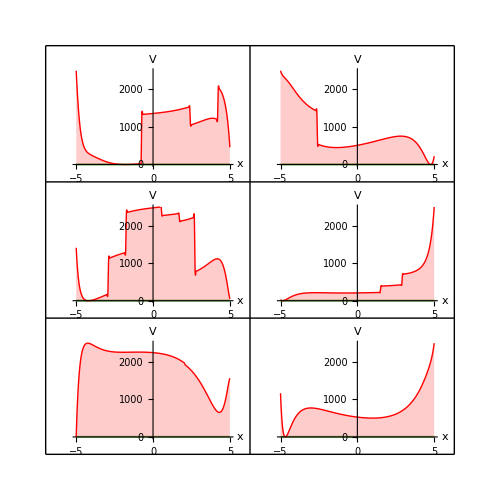

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Code

Written Content / Lesson Plans

Conclusions in Detail

All Visualizations

Data Sources Links/References

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

Education

Physics

Simulation

Quantum Mechanics

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```